# author : Alexei Prokudin email : prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/tmdcollaboration22

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1.01 (06/05/2018)

e-mail: prokudin@jlab.org, kemal.tezgin@uconn.edu

https://github.com/prokudin/WW-SIDIS

If you use this package, please, site Bastami:2018xqd for this paper and https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

Contains the following constants:

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

```mathematica
?wwsidis`*
```

Unpolarized parton distribution functions:

```mathematica
?f1u
?f1d
```

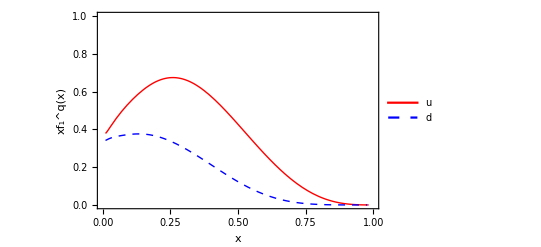

RGBColor[1, 0, 0]If you use these functions, please, cite bibitem{Martin:2009iq}RGBColor[1, 0, 0]

```mathematica
Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
Print[Red,"If you use these functions, please, cite bibitem{Martin:2009iq}",Red]
```

Sivers asymmetry:

```mathematica
?AUTSivers
```

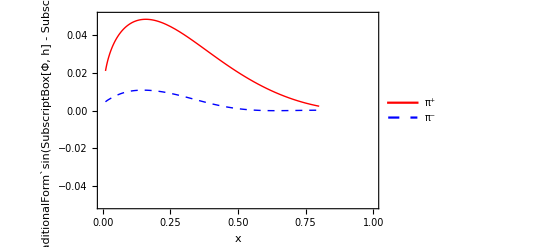

```mathematica
xbj = 0.3; (*x Bjorken*)
zh = 0.3; (*z hadron*)
Q2 = 2.4; (*Q2*)
pT = 0.5; (* hadron transverse momentum *)
Plot[{AUTSivers["pi+",x,zh,Q2, pT],AUTSivers["pi-",x,zh,Q2, pT]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```

Collins asymmetry:

```mathematica
?AUTCollins
```

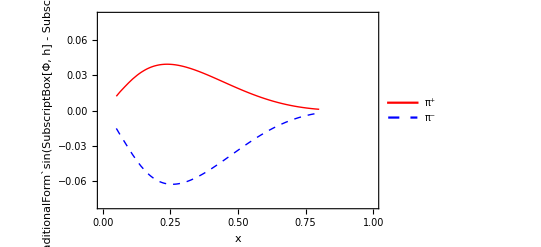

```mathematica
xbj = 0.3; (*x Bjorken*)
zh = 0.3; (*z hadron*)
Q2 = 2.4; (*Q2*)
pT = 0.5; (* hadron transverse momentum *)
Plot[{AUTCollins["pi+",x,zh,Q2, pT],AUTCollins["pi-",x,zh,Q2, pT]},{x,0.05,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.},{-0.08,0.08}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```